```mathematica
(* This file shows Smoldyn's result for 2 sizes of hard spheres.  It analyzes the results of crowding2size.txt. *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/INI/Smoldyn/excludedvolume

```mathematica
maxradius=20
volume=1000000
r1=2.2
r2=4
number1=6000
number2=500
```

20

1000000

2.2

4

6000

500

```mathematica
volfraction=N[(number1*4/3*Pi*r1^3+number2*4/3*Pi*r2^3)/volume]
```

0.401655

```mathematica
(* Load and look at data *)
```

```mathematica
simdata=Import["crowding2sizeout.txt","CSV"];
```

```mathematica
simdata
```

{{5.5,0,0,0,0,0,0,0,0,0,0,0.0000180311,0,0,0,9.4585×10^-6,0,7.30515×10^-6,0.0000194831,0,0,4.733×10^-6,0.0000129091,3.9291×10^-6,0.0000144075,0.0000132555,0.0000244728,0.0000198283,0.000049977,0.000191025,0.000699465,0.00300875,0.0188312,0.0175471,0.0142055,0.0117996,0.00980091,0.00859484,0.00734757,0.00644744,0.00577451,0.00548075,0.00493913,0.00473588,0.00461737,0.00447247,0.00463647,0.00449716,0.00478329,0.00495005,0.0052376,0.00573039,0.00591131,0.00633353,0.00670158,0.00688991,0.00679952,0.00665818,0.00662718,0.00641359,0.00619477,0.00611071,0.00599093,0.00588784,0.00572261,0.00573065,0.00574573,0.00575418,0.00587574,0.00584324,0.00592465,0.0059487,0.00612514,0.00620751,0.00625003,0.00631277,0.00630649,0.00621715,0.00614783,0.00619753,0.00613703,0.00608497,0.0060369,0.00602326,0.0059686,0.0059697,0.00593892,0.00597017,0.00593869,0.00603791,0.00600184,0.00608563,0.00600086,0.00601132,0.00606958,0.0060866,0.0061005,0.00610098,0.00605118,0.00607104,0.00608928}}

```mathematica
simdata1=Drop[simdata[[1]],1]
```

{0,0,0,0,0,0,0,0,0,0,0.0000180311,0,0,0,9.4585×10^-6,0,7.30515×10^-6,0.0000194831,0,0,4.733×10^-6,0.0000129091,3.9291×10^-6,0.0000144075,0.0000132555,0.0000244728,0.0000198283,0.000049977,0.000191025,0.000699465,0.00300875,0.0188312,0.0175471,0.0142055,0.0117996,0.00980091,0.00859484,0.00734757,0.00644744,0.00577451,0.00548075,0.00493913,0.00473588,0.00461737,0.00447247,0.00463647,0.00449716,0.00478329,0.00495005,0.0052376,0.00573039,0.00591131,0.00633353,0.00670158,0.00688991,0.00679952,0.00665818,0.00662718,0.00641359,0.00619477,0.00611071,0.00599093,0.00588784,0.00572261,0.00573065,0.00574573,0.00575418,0.00587574,0.00584324,0.00592465,0.0059487,0.00612514,0.00620751,0.00625003,0.00631277,0.00630649,0.00621715,0.00614783,0.00619753,0.00613703,0.00608497,0.0060369,0.00602326,0.0059686,0.0059697,0.00593892,0.00597017,0.00593869,0.00603791,0.00600184,0.00608563,0.00600086,0.00601132,0.00606958,0.0060866,0.0061005,0.00610098,0.00605118,0.00607104,0.00608928}

```mathematica
nbin=Length[simdata1]
```

100

```mathematica
binwidth=N[maxradius/nbin]
```

0.2

```mathematica
simdata2=simdata1/(number2/volume)
```

{0,0,0,0,0,0,0,0,0,0,0.0360622,0,0,0,0.018917,0,0.0146103,0.0389662,0,0,0.009466,0.0258182,0.0078582,0.028815,0.026511,0.0489456,0.0396566,0.099954,0.38205,1.39893,6.0175,37.6624,35.0942,28.411,23.5992,19.6018,17.1897,14.6951,12.8949,11.549,10.9615,9.87826,9.47176,9.23474,8.94494,9.27294,8.99432,9.56658,9.9001,10.4752,11.4608,11.8226,12.6671,13.4032,13.7798,13.599,13.3164,13.2544,12.8272,12.3895,12.2214,11.9819,11.7757,11.4452,11.4613,11.4915,11.5084,11.7515,11.6865,11.8493,11.8974,12.2503,12.415,12.5001,12.6255,12.613,12.4343,12.2957,12.3951,12.2741,12.1699,12.0738,12.0465,11.9372,11.9394,11.8778,11.9403,11.8774,12.0758,12.0037,12.1713,12.0017,12.0226,12.1392,12.1732,12.201,12.202,12.1024,12.1421,12.1786}

```mathematica
simdata2=simdata2/simdata2[[-1]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00296112,0.,0.,0.,0.0015533,0.,0.00119967,0.00319957,0.,0.,0.000777268,0.00211997,0.000645249,0.00236604,0.00217686,0.004019,0.00325626,0.00820737,0.0313707,0.114868,0.494106,3.09252,2.88164,2.33287,1.93777,1.60954,1.41147,1.20664,1.05882,0.948308,0.900065,0.811119,0.777741,0.758278,0.734483,0.761415,0.738537,0.785526,0.812912,0.860135,0.941062,0.970773,1.04011,1.10055,1.13148,1.11664,1.09343,1.08834,1.05326,1.01732,1.00352,0.983849,0.966919,0.939784,0.941105,0.943581,0.944969,0.964932,0.959595,0.972964,0.976914,1.00589,1.01942,1.0264,1.0367,1.03567,1.021,1.00962,1.01778,1.00784,0.999292,0.991398,0.989158,0.980182,0.980362,0.975307,0.980439,0.97527,0.991564,0.98564,0.999401,0.985479,0.987197,0.996765,0.99956,1.00184,1.00192,0.993743,0.997005,1.}

```mathematica
xvector=Table[i,{i,binwidth/2,maxradius-binwidth/2,binwidth}]
```

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1,2.3,2.5,2.7,2.9,3.1,3.3,3.5,3.7,3.9,4.1,4.3,4.5,4.7,4.9,5.1,5.3,5.5,5.7,5.9,6.1,6.3,6.5,6.7,6.9,7.1,7.3,7.5,7.7,7.9,8.1,8.3,8.5,8.7,8.9,9.1,9.3,9.5,9.7,9.9,10.1,10.3,10.5,10.7,10.9,11.1,11.3,11.5,11.7,11.9,12.1,12.3,12.5,12.7,12.9,13.1,13.3,13.5,13.7,13.9,14.1,14.3,14.5,14.7,14.9,15.1,15.3,15.5,15.7,15.9,16.1,16.3,16.5,16.7,16.9,17.1,17.3,17.5,17.7,17.9,18.1,18.3,18.5,18.7,18.9,19.1,19.3,19.5,19.7,19.9}

```mathematica
Length[xvector]
```

100

```mathematica
simdata2xy=Transpose[{xvector,simdata2}];
```

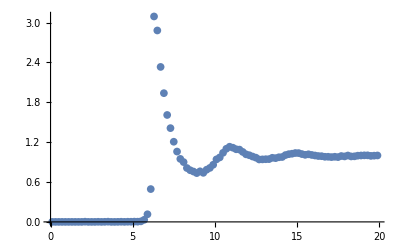

```mathematica
ListPlot[simdata2xy,PlotRange->All]
```